# Phasenraum für Pendel mittels 4th-Order Runge Kutta

20241

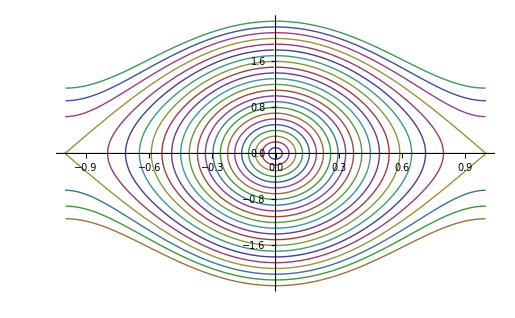

```mathematica
f[u_]:={u[[2]]/Pi,-Sin[u[[1]]*Pi]}
h=0.01;p=2.3;nS=23;n=0;Z=0;u={0,p};U={{u}};P=p;j=3;
Do[
	Z++;

	While[ If[0<=u[[2]] && u[[1]]<0,(p-u[[2]])/p>0.0001 ,True] ,n++;
		k0=h*f[u];k1=h*f[u+k0/2];k2=h*f[u+k1/2];k3=h*f[u+k2];
		u+=1/6*(k0+2*k1+2*k2+k3);If[u[[1]]>1,u[[1]]-=2 ];
	AppendTo[U[[Z]],u];];

	p-=P/nS;
	
	u={0,p};AppendTo[U,{u}];

,{nS}]

n
k=Table[Sort[U[[i]],#1[[1]]<#2[[1]]&],{i,1,j}];
kk=Join[Table[U[[nS-i+1]],{i,1,nS-j}],k,Table[{#[[1]],-#[[2]]}&/@k[[i]],{i,1,j}]];
ListPlot[kk,Joined->True]
```